```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Import Data

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Vdata=SplitBy[Import["latticedata/AllData2p1Flavors/Vall.txt","Table"],First];

ReVdataT[n_]:=Table[Vdata[[n,x,2;;3]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataT[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTe[n_]:=Table[Vdata[[n,x,2;;4]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataTe[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]],Vdata[[n,x,6]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTn[n_]:=ReVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ImVdataTn[n_]:=ImVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ReVdataTne[n_]:=ReVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};
ImVdataTne[n_]:=ImVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};

T0data=Join[{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT41.05.dat","Table"][[All,1;;3]]},{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT71.54.dat","Table"][[All,1;;3]]}];
T0data=T0data/.{a_,b_,c_}:>{a/0.197327,b,c};
```

## Define functions for real part

```mathematica
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c
ReVm0[r_,α_,σ_,c_]:=c-α/r+σ r;
```

## Low T Cornell Fitting & Interpolation

```mathematica
T0datarand[n_]:=Table[{T0data[[n]][[i,1]],RandomVariate[NormalDistribution[T0data[[n]][[i,2]],T0data[[n]][[i,3]]]]},{i,Length[T0data[[n]]]}]
```

### beta = 6.9 Fitting

```mathematica
VaryFitLow=Range[2,4];
VaryFitHigh=Range[20,28];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];

VaryFitLowAR={2,2,2,2,2,1,3,1,3}+1;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}-2;
```

#### Varied Weights (not in use)

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

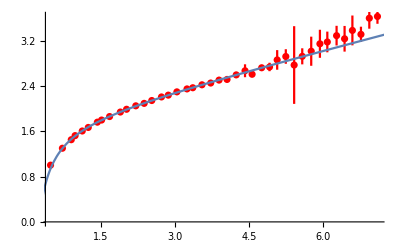

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

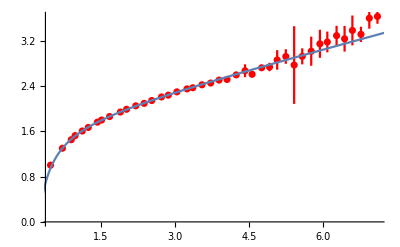

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

-Graphics-

#### Use this one!

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

-Graphics-

### beta = 7.4 Fitting

```mathematica
VaryFitLow=Range[5,7];
VaryFitHigh=Range[26,34];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
```

```mathematica
VaryFitLowAR={2,2,2,2,2,1,3,1,3}+4;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}+4;
```

#### Varied Weights (not in use)

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

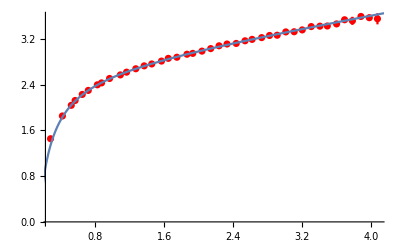

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

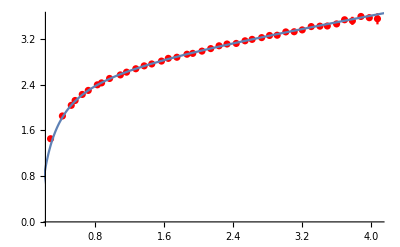

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

-Graphics-

#### Use this one!

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

-Graphics-

### Linear Interpolation

```mathematica
β={6.8,6.9,7,7.125,7.25,7.3,7.48};
T={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
```

```mathematica
btinter=Interpolation[Transpose[{T,β}]];
```

```mathematica
beta2T0res={αfinal69,σfinal69,cfinal69};
beta7T0res={αfinal748,σfinal748,cfinal748};
```

```mathematica
T0constfit={LinearModelFit[{{β[[2]],beta2T0res[[1,1]]},{β[[7]],beta7T0res[[1,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,1]]},{β[[7]],beta7T0res[[2,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,1]]},{β[[7]],beta7T0res[[3,1]]}},x,x]};
T0errfit={LinearModelFit[{{β[[2]],beta2T0res[[1,2]]},{β[[7]],beta7T0res[[1,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,2]]},{β[[7]],beta7T0res[[2,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,2]]},{β[[7]],beta7T0res[[3,2]]}},x,x]};
```

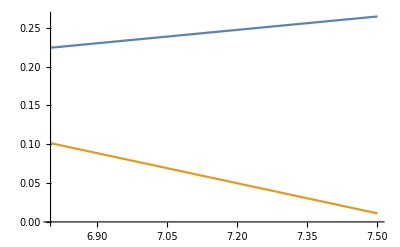

```mathematica
Plot[{T0constfit[[2]][x],T0errfit[[3]][x]},{x,6.8,7.5}]
```

```mathematica
Tscan=Table[i,{i,0.15,0.25,0.003}]
```

{0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249}

```mathematica
βTscan=Table[btinter[i],{i,0.15,0.25,0.003}]
```

{6.81385,6.8325,6.85091,6.86907,6.887,6.9047,6.92218,6.93945,6.95652,6.97339,6.99007,7.00662,7.02305,7.03931,7.05539,7.0713,7.08702,7.10256,7.1179,7.13291,7.1476,7.16212,7.17648,7.19072,7.20484,7.21888,7.23284,7.24676,7.26075,7.2747,7.28855,7.30228,7.31589,7.32936}

```mathematica
Table[T0constfit[[2]][βTscan[[i]]],{i,1,Length[βTscan]}]
```

{0.22519,0.226263,0.227322,0.228367,0.229399,0.230417,0.231423,0.232417,0.233399,0.23437,0.23533,0.236282,0.237227,0.238162,0.239088,0.240003,0.240908,0.241802,0.242685,0.243548,0.244393,0.245229,0.246055,0.246874,0.247687,0.248495,0.249298,0.250099,0.250904,0.251707,0.252503,0.253294,0.254077,0.254852}

```mathematica
Table[T0errfit[[2]][βTscan[[i]]],{i,1,Length[βTscan]}]
```

{0.0300814,0.0293596,0.0286475,0.0279448,0.0272512,0.0265664,0.0258901,0.0252219,0.0245616,0.0239088,0.0232632,0.0226231,0.0219875,0.0213584,0.0207361,0.0201208,0.0195124,0.0189113,0.0183175,0.0177369,0.0171686,0.0166069,0.0160511,0.0155003,0.0149538,0.0144108,0.0138705,0.0133322,0.0127907,0.012251,0.0117153,0.011184,0.0106575,0.0101363}

## Debye Fitting

```mathematica
ReVdataTnrand[n_]:=Table[{ReVdataTne[n][[i,1]],RandomVariate[NormalDistribution[ReVdataTne[n][[i,2]],ReVdataTne[n][[i,3]]]]},{i,Length[ReVdataTne[n]]}]
```

```mathematica
T0constrand[n_]:={RandomVariate[NormalDistribution[T0constfit[[1]][β[[n]]],T0errfit[[1]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[2]][β[[n]]],T0errfit[[2]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[3]][β[[n]]],T0errfit[[3]][β[[n]]]]]}
```

```mathematica
VaryFitLow=Range[1,3];
VaryFitHigh=Range[18,30];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
fitrandall[n_]:=ParallelTable[Quiet[m/.NonlinearModelFit[ReVdataTnrand[n][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReV[r,m,T0constrand[n][[1]],T0constrand[n][[2]],T0constrand[n][[3]]],{{m,0.1}},r, MaxIterations->1000]["BestFitParameters"]],{ii,1,1000},{i,1,Length[VaryFit]}];
mdfitrandres=ConstantArray[0,Length[Vdata]];
mdfitrandfinal=ConstantArray[0,Length[Vdata]];
```

```mathematica
Do[mdfitrandres[[n]]=fitrandall[n],{n,Length[mdfitrandres]}]//AbsoluteTiming
Do[mdfitrandfinal[[n]]={Mean[Flatten[mdfitrandres[[n]]]],StandardDeviation[Flatten[mdfitrandres[[n]]]]},{n,Length[mdfitrandres]}];
mdfitrandfinal
```

{3914.32,Null}

{{0.0651261,0.101466},{0.142497,0.142256},{0.195636,0.161515},{0.309553,0.207166},{0.479356,0.168118},{0.496861,0.189719},{0.652941,0.152739}}

```mathematica
mdfinal
```

{{0.0128579,0.0271323},{0.120289,0.0538736},{0.190378,0.0591668},{0.310912,0.131682},{0.481991,0.053005},{0.495937,0.111125},{0.65067,0.0974602}}

```mathematica
Manipulate[Show[{Plot[{ReV[r,mdfitrandfinal[[n,1]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]]],ReV[r,mdfitrandfinal[[n,1]]+mdfitrandfinal[[n,2]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]]],ReV[r,If[mdfitrandfinal[[n,1]]-mdfitrandfinal[[n,2]]>0,mdfitrandfinal[[n,1]]-mdfitrandfinal[[n,2]],0.0000000001],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]]]},{r,0,5}],ErrorListPlot[ReVdataTne[n],PlotRange->All,PlotStyle->{Red}]}],{n,1,Length[mdfitrandfinal],1}]
```

## Plotting of imaginary part

```mathematica
g[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
ϕ[x_]:=Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[x z],{z,0,∞}]];
```

```mathematica
ϵ=1/1000;
ϕ1table10=Quiet[ Join[Parallelize[Table[{x,1-ϕ[x]},{x,ϵ/100,2,10ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,2+100ϵ,10,100ϵ}]]]];
ϕ110=Interpolation[ϕ1table10];
```

```mathematica
Do[
Module[{σ=T0constfit[[2]][β[[n]]], α=T0constfit[[1]][β[[n]]],mD=mdfitrandfinal[[n,1]],c,r,μ},
μ=(mD^2 σ/α)^(1/4);
r=mD/μ;
pg=1;
c=Re[ParabolicCylinderD[-1/2,ⅈ ϵ/100]NIntegrate[ParabolicCylinderD[-1/2,√2 x] x^2 g[x r],{x,0,∞}]];
ψ1[x_,r_]:=c-ParabolicCylinderD[-1/2,√2 x]NIntegrate[y^2 g[y r]Re[ParabolicCylinderD[-1/2,ⅈ √2 y]],{y,0,x},PrecisionGoal->pg]-Re[ParabolicCylinderD[-1/2,ⅈ √2 x]]NIntegrate[ParabolicCylinderD[-1/2,√2 y] y^2 g[y r],{y,x,∞},PrecisionGoal->pg];
ψ1table10[n]=Join[Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,ϵ/100,1,10ϵ}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,1+100ϵ,10+ϵ,100ϵ}]]];],{n,1,Length[Vdata]}]
```

$Aborted

```mathematica
ImV[x_,n_]:=T0constfit[[1]][β[[n]]] T[[n]] ϕ110[mdfitrandfinal[[n,1]] x]+T0constfit[[1]][β[[n]]] T[[n]] Interpolation[ψ1table10[n]][(mdfitrandfinal[[n,1]]^2(T0constfit[[2]][β[[n]]])/(T0constfit[[1]][β[[n]]]))^(1/4) x];
```

```mathematica
(*Manipulate[Show[Plot[{ImV[x,n],ImVar[x,n]},{x,0,10}],ErrorListPlot[ImVdataTne[n]],PlotRange->All],{n,1,Length[ReVdata],1}]*)
```